1. Basic functions in mathStatica:

"function " | "description "
PlotDensity[ f ]        | Plotting (automated)
Expect[x,f ]  | Expectation operator        E[X] 
Prob[x,f] | Probability       	      P(X≤x)
Transform[eqn,f ]       | Transformations

Here:  random variable X with density f(x). Note: "density" could be also discrete. Example:

```mathematica
f =1/(π √(1-x) √x);           domain[f] = {x,0,1};
```

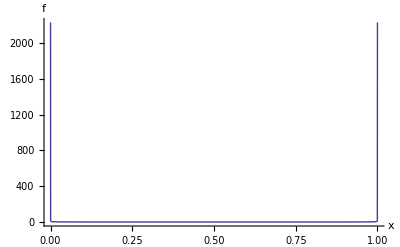

```mathematica
PlotDensity[f]
```

To get the analytic form of the CDF, Expected value and Variance:

```mathematica
Prob[x,f]
```

Piecewise[{{1, x≥1}, {(2 ArcSin[√x])/π, 0<x<1}, {0, True}}]

```mathematica
Expect[x,f]
```

1/2

```mathematica
Var[x,f]
```

1/8

The r^th moment of X is E[X^r]:

```mathematica
Expect[x^r,f]
```

This further assumes that: {r>-1/2}

Γ[1/2+r]/(√π Γ[1+r])

Now consider the transformation to a new random variable Y such that Y=√X. By using the Transform and TransformExtremum functions, the pdf of Y, say g(y), and the domain of its support can be found
(but note: one-to-oneness must be guaranteed)

```mathematica
g = Transform[y ==√x, f]
```

2/(π √(1-y^2))

```mathematica
domain[g] = TransformExtremum[y ==√x, f]
```

{y,0,1}

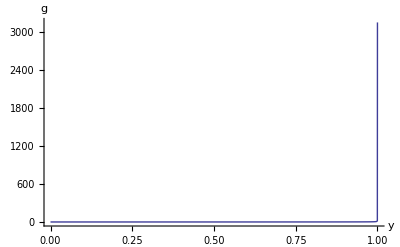

```mathematica
PlotDensity[g]
```

mathStatica has been designed to support parameters; their domain is included in the domain definition for the density

```mathematica
f   =   1/(σ √(2 π))Exp[-(x - μ)^2/(2 σ^2)];
domain[f] = {x, -∞, ∞} && {μ∈Reals, σ>0}; (* Note:could have used {μ,-∞,∞} or 
-∞<μ<∞   instead !*)
```

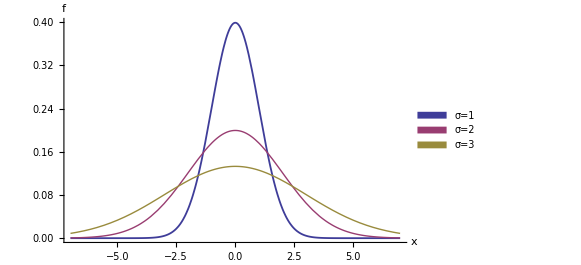

```mathematica
PlotDensity[f /.{μ->0,σ->{1,2,3}}]
```

```mathematica
Expect[x,f] 
 Var[x,f]
Var[x^2,f]
```

μ

σ^2

2 (2 μ^2 σ^2+σ^4)

```mathematica
M=Expect[ⅇ^(t x),f] (* The moment generating function *)
```

ⅇ^(t μ+(t^2 σ^2)/2)

```mathematica
FisherInformation[μ,f]
Sufficient[f,i,n] (* helps us to inspect the joint distribution and
to identify sufficient statistic *)
```

1/σ^2

ⅇ^(-(n μ^2-2 μ ∑_(i=1)^n x_i+∑_(i=1)^n x_i^2)/(2 σ^2)) (2 π)^(-n/2) σ^-n

```mathematica
(* Our old friend: Bernoulli distribution *)
f=p^x(1-p)^(1-x) 
domain[f]={x,0,1}&&{0<p<1}&&{Discrete};
Expect[x,f]
Var[x,f]
FisherInformation[p,f]
1/(n  FisherInformation[p,f])  (* which is the CRLB *)
```

(1-p)^(1-x) p^x

p

-(-1+p) p

1/(p-p^2)

(p-p^2)/n

```mathematica
(* more involved discrete distribution *)
f=Binomial[r+x-1,x] p^r (1-p)^x  (* number x of failures until r-th success *)
domain[f]={x,0,∞} && {Discrete} && {0<p<1, r>0, r∈Integers}
```

(1-p)^x p^r Binomial[-1+r+x,x]

{x,0,∞}&&{Discrete}&&{0<p<1,r>0,r∈Integers}

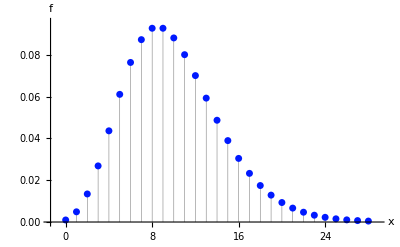

```mathematica
PlotDensity[f /. {p->0.5,r->10}]
```

```mathematica
Prob[x,f]
Expect[x,f]
Var[x,f]
Expect[t^x,f] (* The probability generating function *)
FisherInformation[p,f]
1/(n  FisherInformation[p,f])
```

Piecewise[{{1+(1-p)^Floor[x] (-1+p) p^r Binomial[r+Floor[x],1+Floor[x]] Hypergeometric2F1[1,1+r+Floor[x],2+Floor[x],1-p], x≥0}, {0, True}}]

(-1+1/p) r

(r-p r)/p^2

p^r (1+(-1+p) t)^-r

-r/((-1+p) p^2)

-((-1+p) p^2)/(n r)

```mathematica
(* Now we want to calculate the CRLB for estimating the parameter
lambda (the Expecteed value) of the Poisson distribution: *)
f=(ⅇ^-λ λ^x)/(x!);         domain[f]={x,0,∞}&&{λ>0}&&{Discrete};
1/(n  FisherInformation[λ,f])
(* We can also get a sufficient statistic by inspecting how the
joint distribution is factorised: *)
Sufficient[f,i,n]
```

λ/n

ⅇ^(-n λ) λ^(∑_(i=1)^n x_i) ∏_(i=1)^n 1/(x_i!)

```mathematica
(* multivariate rv can also be treated: (Gumbel)*)            f   =  ⅇ^(-2 (x+y)) (ⅇ^(x+y)+α(ⅇ^x-2) (ⅇ^y-2));
domain[f] = {{x,0,∞}, {y,0,∞}}  &&  {-1<α<1};
```

```mathematica
Plot3D[f /.α->-0.8,{x,0,2},{y,0,3}]
(* Note: PlotDensity works only on functions of one argument but we can use Mathematica's Plot3D *)
```

-Graphics3D-

```mathematica
Prob[{x,y},f]
Cov[{x,y},f]
Varcov[f]
Marginal[x,f]
Conditional[y,f]
mgf=Expect[Exp[Subscript[t, 1] x + Subscript[t, 2] y], f]
```

Piecewise[{{ⅇ^(-2 (x+y)) (-1+ⅇ^x) (-1+ⅇ^y) (ⅇ^(x+y)+α), x>0&&y>0}, {0, True}}]

α/4

(1 | α/4
α/4 | 1)

Piecewise[{{ⅇ^-x, x>0}, {0, True}}]

Here is the conditional pdf f(y|x):

Piecewise[{{ⅇ^(x-2 (x+y)) (ⅇ^(x+y)+(-2+ⅇ^x) (-2+ⅇ^y) α), y>0}, {0, True}}]

This further assumes that: {t_1<1,t_2<1}

(4-2 t_2+t_1 (-2+(1+α) t_2))/((-2+t_1) (-1+t_1) (2-3 t_2+t_2^2))

```mathematica
(* The power of the Manipulate command. The command below illustrates too many additional options of the Plot3D command to make "the ultimate plot". If you just want to see the
simple effect of Manipulate you can go over directly to the next command. *)
Manipulate[
Plot3D[ⅇ^(-2 (x+y)) (ⅇ^(x+y)+α(ⅇ^x-2) (ⅇ^y-2)), {x, 0, 2}, {y, 0, 3}, 
AxesLabel -> {"
StyleBox[\"x\",\nFontSlant->\"Italic\"]", "
StyleBox[\"y\",\nFontSlant->\"Italic\"]", "
StyleBox[\"f\",\nFontSlant->\"Italic\"]"},AspectRatio->1,PlotRange->{0,1}, Ticks-> {{0,1,2}, {0, 1}, {0, .5}},ImageSize -> 450, PerformanceGoal -> "Quality",PlotLabel -> Style[StringJoin["α = ", ToString[PaddedForm[α,{3,2}]]], FontColor -> Red, FontSize ->14]], 
{{α,-0.8},-1,0}]
```

```mathematica
(* Or MORE SIMPLY *)
Manipulate[Plot3D[ⅇ^(-2 (x+y)) (ⅇ^(x+y)+α (ⅇ^x-2) (ⅇ^y-2)),{x,0,2},{y,0,3}],{{α,-0.8},-1,0}]
```

```mathematica
(*2. Fisher information matrix
whenever possible to calculate explicitly, for example for inverse Gaussian : *)
             f  =√(λ/(2 π x^3)) Exp[-λ (x-μ)^2/(2 μ^2 x)];   
domain[f] = {x,0,∞} && {μ>0,λ>0};
FisherInformation[{μ,λ},f]
```

(λ/μ^3 | 0
0 | 1/(2 λ^2))

{139.8,141.,139.5,141.7,140.2,142.2,140.3,142.,139.7,141.8,139.9,141.4,140.2,141.6,139.9,141.7,139.4,141.9,140.3,140.7,139.2,141.8,140.1,142.2,140.6,141.4,139.9,141.7,139.7,141.8,139.2,141.6,139.8,141.7,139.9,141.9,140.,141.5,139.2,141.9,139.6,141.4,139.6,141.6,140.2,141.5,139.7,141.6,140.1,141.1,139.6,142.3,140.2,142.4,140.,141.9,140.3,141.8,139.9,142.,139.8,141.8,139.2,142.3,139.9,140.7,139.7,141.,139.5,141.4,139.5,141.8,139.4,141.8,138.3,142.,139.8,142.1,139.6,141.3,139.3,142.3,139.2,140.9,139.9,141.7,139.9,140.9,139.3,141.,139.8,141.8,139.9,141.5,138.1,142.,139.4,141.1,139.4,142.,139.8,141.3,139.,141.1,139.3,140.9,139.4,141.6,139.5,141.4,139.7,142.,139.5,141.2,139.2,141.1,139.3,141.3,137.9,141.4,138.4,141.6,138.1,141.5,139.5,141.5,139.1,141.4,139.8,141.5,139.7,140.8,138.8,141.3,138.6,141.5,139.6,141.8,139.7,139.6,137.8,140.9,139.6,141.4,139.4,141.2,139.2,141.8,139.6,142.1,139.,141.7,139.7,141.2,139.6,141.,139.1,140.9,137.8,141.8,139.1,140.6,138.7,141.,139.3,141.9,139.3,141.3,139.5,141.2,139.4,141.5,138.5,141.6,139.2,142.1,139.4,141.5,139.2,142.,139.4,141.6,138.6,141.4,139.2,141.5,138.5,141.5,139.8,142.,139.6,141.7,139.7,141.1,140.,141.2,139.4,141.5,139.6,141.2}

0.200059

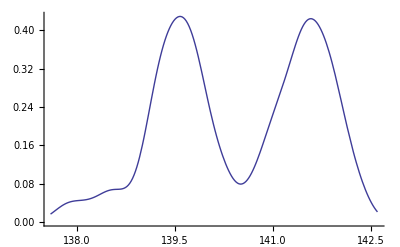

```mathematica
(* 3. Now: non-parametric density estimation: *)
data=ReadList["sd.dat"]
f=(ⅇ^(-x^2/2))/(√(2 π));        domain[f] ={x,-∞,∞}; (* defines the kernel *)
c=Bandwidth[data,f,Method->SheatherJones]
NPKDEPlot[data,c,f]
```

```mathematica
(* 4.1. Symbolic MLE for normal*)
f = 1/(σ √(2 π))Exp[-(x-μ)^2/(2 σ^2)];      domain[f]={x,-∞,∞}&&{μ∈Reals,σ>0};
SuperLog[On] (* Note: SuperLog modifies Mathematica’s Log functionso that Log[Product[]]‘objects’ or ‘terms’ get converted into sums of logarithms. *)
logLθ=Log[∏_(i=1)^n (f/.x->Subscript[x, i])]
score=Grad[logLθ,{μ,σ}]
solθ=Solve[score==0,{μ,σ}]
solθ=solθ[[2]]
Eigenvalues[Hessian[logLθ,{μ,σ}]/.solθ]//Simplify
```

SuperLog is now On.

-(n (μ^2+σ^2 Log[2 π]+2 σ^2 Log[σ])-2 μ ∑_(i=1)^n x_i+∑_(i=1)^n x_i^2)/(2 σ^2)

{(-n μ+∑_(i=1)^n x_i)/σ^2,(n μ^2-n σ^2-2 μ ∑_(i=1)^n x_i+∑_(i=1)^n x_i^2)/σ^3}

{{μ→(∑_(i=1)^n x_i)/n,σ→-(√(-(∑_(i=1)^n x_i)^2+n ∑_(i=1)^n x_i^2))/n},{μ→(∑_(i=1)^n x_i)/n,σ→(√(-(∑_(i=1)^n x_i)^2+n ∑_(i=1)^n x_i^2))/n}}

{μ→(∑_(i=1)^n x_i)/n,σ→(√(-(∑_(i=1)^n x_i)^2+n ∑_(i=1)^n x_i^2))/n}

{(2 n^3)/((∑_(i=1)^n x_i)^2-n ∑_(i=1)^n x_i^2),n^3/((∑_(i=1)^n x_i)^2-n ∑_(i=1)^n x_i^2)}

```mathematica
(* 4.2. Symbolic MLE-second example *) 
L =  ∏_(i=1)^n Subscript[x, i]/σ^2 Exp[-Subscript[x, i]^2/(2 σ^2)];(* Rayleigh(σ) *)
SuperLog[On]
logL=Log[L]
FOC=D[logL,{σ,1}] (* From First Order Conditions *)
σ̂=Solve[FOC==0,σ][[2]]
SOC=D[logL,{σ,2}]/. σ̂ (* From Second Order Conditions *)
data={1,6,3,4}
σ̂/. {n->4,Subscript[x, i_]:>data[[i]]}
(* This is rule delayed *)
SuperLog[Off]
```

SuperLog is now On.

-2 n Log[σ]+∑_(i=1)^n Log[x_i]-(∑_(i=1)^n x_i^2)/(2 σ^2)

-(2 n)/σ+(∑_(i=1)^n x_i^2)/σ^3

{σ→(√(∑_(i=1)^n x_i^2))/(√2 √n)}

-(8 n^2)/(∑_(i=1)^n x_i^2)

{1,6,3,4}

{σ→(√31)/2}

SuperLog is now Off.

```mathematica
(* 5. Densities of Order statistics *)
```

```mathematica
f = ⅇ^-x/((1+ⅇ^-x)^2);     domain[f]={x,-∞,∞};
OrderStat[r,f]
OrderStat[{r,s},f]
```

((1+ⅇ^-x)^-r (1+ⅇ^x)^(-1-n+r) n!)/((n-r)! (-1+r)!)

Piecewise[{{(ⅇ^x_s (1+ⅇ^x_r)^-s (1+ⅇ^x_s)^(-1-n+r) (-ⅇ^x_r+ⅇ^x_s)^(-1+s) (-1+ⅇ^(-x_r+x_s))^-r n!)/((-1+r)! (n-s)! (-1-r+s)!), x_r<x_s}, {0, True}}]

```mathematica
(* Order stat works also on piece-wise continuous functions. The Laplace distribution with parameters μ,σ
has its density defined piece-wise for values of the argument < and > μ.
The density of the r-th order statistic is also defined piece-wise : *)
f=If[x<μ,ⅇ^((x - μ)/σ)/(2σ),ⅇ^(-(x - μ)/σ)/(2σ)];

domain[f]={x,-∞,∞} && {μ∈Reals, σ>0};
OrderStat[r,f]
```

If[x<μ,(2^-r ⅇ^((r (x-μ))/σ) (1-1/2 ⅇ^((x-μ)/σ))^(n-r) n!)/(σ (n-r)! (-1+r)!),(2^(-1-n+r) ⅇ^(((1+n-r) (-x+μ))/σ) (1-1/2 ⅇ^((-x+μ)/σ))^(-1+r) n!)/(σ (n-r)! (-1+r)!)]